```mathematica
ClearAll["Global`*"]
ClearSystemCache[]
```

```mathematica
Sfunc[dp_,ptot_,kp_,KMM_]:=(dp*ptot/kp)/(KMM+(dp*ptot/kp));
Rfunc[dm_,dmmu_,KMM_,mutot_,ptot_,dp_,kp_]:=1-1/(1+(dm+dmmu)/dm*mutot/(KMM+dp*ptot/kp));
fcm[dm_,R_,S_]:=dm*(1-R*S)/(1-R);

(*Actual Fano Factor for Regulated SyScem*)
fanofuncmuraw[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{R,S,cm,er0},
R=Rfunc[dm,dmmu,KMM,mutot,ptot,dp,kp];
     S=Sfunc[dp,ptot,kp,KMM];
cm=fcm[dm,R,S];
er0=1+kp/(1-R*S)/(dp+cm)+ptot/mutot*(R/(1-R*S))^2*(dp*cm)*(cm+dp+dmu)/((dp+cm)(cm+dmu)(dp+dmu));
Return[er0];]

(*Actual Fano Factor for Unregulated SyScem*)
fanounregfunc[kp_,dp_,dm_,ptot_]:=1+kp/(dm+dp);

(*Optimal Fano Factor for Regulated SyScem*)
foptfuncmuraw2[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{Rqq,Sqq,etaw,zetaw,Qw,smu1w,smu2w,eres2},Rqq=Rfunc[dm,dmmu,KMM,mutot,ptot,dp,kp];
Sqq=Sfunc[dp,ptot,kp,KMM];
etaw=(1-Rqq)/(Rqq)/(1-Sqq)^2;
zetaw=dm/(dm+dmmu);
Qw=etaw*Sqq/zetaw;
smu1w=Sqrt[(dmu^2 etaw+dm^2 (1+etaw)+dm dmu Qw+Sqrt[-4 dm^2 dmu etaw (dmu+dmu etaw+dm Qw)+(dmu^2 etaw+dm^2 (1+etaw)+dm dmu Qw)^2])/etaw]/Sqrt[2];
smu2w=Sqrt[(dmu^2 etaw+dm^2 (1+etaw)+dm dmu Qw-Sqrt[-4 dm^2 dmu etaw (dmu+dmu etaw+dm Qw)+(dmu^2 etaw+dm^2 (1+etaw)+dm dmu Qw)^2])/etaw]/Sqrt[2];
eres2=(dm+dp+kp+(dm^2 kp (((dm+dmu) dp ((-dm-dmu) (dm-dp) (dm+dp)-(4 dm (dmu+dp) (dm+smu1w) (dm+smu2w))/(dp+smu1w)))/((dm+smu1w)^2 (dm+smu2w)^2)+(dm (dmu+dp) ((dmu+dp) (-dm^2+dp^2)+(4 (dm+dmu) dp (dp+smu1w) (dp+smu2w))/(dm+smu1w)))/((dp+smu1w)^2 (dp+smu2w)^2)))/((dm-dp)^3 etaw))/(dm+dp);
Return[eres2];]
(*----------------------------------------------*)
```

```mathematica
(*Functions for Minimization*)

(*Error(actual) minimizing K value at fixed nucleotide number c1*)
KMMminndaggernum[c1_,kp_,ptot_,dmmu_,dp_,dm_,dmu_,nm_,nmu_,KMMc_,pbaRc_]:=Module[{sac,KMMcand,sacmat,KMMresf,mutotvar,zetav,mutotval,fanores,KMMv,mutinf,Rget,Sget,c0,gamivar,gamcvar,gamival,gamcval,mnull},
zetav=dm/(dm+dmmu);
{gamivar,gamcvar,mutotvar,mnull}=fixNuctgetgammsnum[c1,kp,KMMv,dp,ptot,zetav,dm,dmu,nm,nmu,KMMv,pbaRc];
sac=fanofuncmuraw[kp,ptot,dp,dm,KMMv,dmmu,mutotvar/(1+gamivar),dmu];
KMMcand=2*dp/kp*ptot;
sacmat=FindMinimum[{sac,KMMv>0},{KMMv,KMMcand},PrecisionGoal->15][[2]];
KMMresf=KMMv/.sacmat[[1]];
mutotval=fixNuctgetmutotnum[c1,kp,KMMresf,dp,ptot,zetav,dm,dmu,nm,nmu,KMMresf,pbaRc];
{gamival,gamcval,mutotval,mnull}=fixNuctgetgammsnum[c1,kp,KMMresf,dp,ptot,zetav,dm,dmu,nm,nmu,KMMresf,pbaRc];
fanores=fanofuncmuraw[kp,ptot,dp,dm,KMMresf,dmmu,mutotval/(1+gamival),dmu];
mutinf=-1/2*Log2[ewk[kp,ptot,dp,dm,KMMresf,dmmu,mutotval/(1+gamival),dmu]];
Rget=Rfunc[dm,dmmu,KMMresf,mutotval/(1+gamival),ptot,dp,kp];
Sget=Sfunc[dp,ptot,kp,KMMresf];
c0=nm*dm*dp/kp*(ptot+pbaRc);
Return[{KMMresf,mutotval,c1,fanores,mutinf,Rget,Sget,c1/c0,c1-c0}];]

fanogap[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{cm,R,S,ress},R=Rfunc[dm,dmmu,KMM,mutot,ptot,dp,kp];
S=Sfunc[dp,ptot,kp,KMM];
cm=fcm[dm,R,S];
ress=(((cm+dm) (cm+dp) (dm+dp)+dm (cm+dm+2 dp) kp))/((cm+dm) (cm+dp) (dm+dp));
Return[ress];]
ewk[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{ff0,ffmu,ffgap,eres,ffdenom},ff0=fanounregfunc[kp,dp,dm,ptot];
ffmu=fanofuncmuraw[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
ffgap=fanogap[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
ffdenom=ff0-2*ffgap+ffmu;
eres=1-(ff0-ffgap)^2/ff0/ffdenom;
Return[eres];]
ewkopt[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{ff0,ffopt,eres},ff0=fanounregfunc[kp,dp,dm,ptot];
ffopt=foptfuncmuraw2[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
eres=(ffopt-1)/(ff0-1);
Return[eres];]

(*Error(optimal) minimizing K value at fixed nucleotide number c1*)
KMMminndaggerOPTnum[c1_,kp_,ptot_,dmmu_,dp_,dm_,dmu_,nm_,nmu_,KMMc_,pbaRc_]:=Module[{sac,KMMcand,sacmat,KMMresf,mutotvar,zetav,mutotval,fanores,KMMv,mutinf,Rget,Sget,c0,gamivar,gamcvar,gamival,gamcval,mnull},
zetav=dm/(dm+dmmu);
{gamivar,gamcvar,mutotvar,mnull}=fixNuctgetgammsnum[c1,kp,KMMv,dp,ptot,zetav,dm,dmu,nm,nmu,KMMv,pbaRc];
sac=foptfuncmuraw2[kp,ptot,dp,dm,KMMv,dmmu,mutotvar/(1+gamivar),dmu];
KMMcand=2*dp/kp*ptot;
sacmat=FindMinimum[{sac,KMMv>0},{KMMv,KMMcand},PrecisionGoal->12][[2]];
KMMresf=KMMv/.sacmat[[1]];
mutotval=fixNuctgetmutotnum[c1,kp,KMMresf,dp,ptot,zetav,dm,dmu,nm,nmu,KMMresf,pbaRc];
{gamival,gamcval,mutotval,mnull}=fixNuctgetgammsnum[c1,kp,KMMresf,dp,ptot,zetav,dm,dmu,nm,nmu,KMMresf,pbaRc];
fanores=foptfuncmuraw2[kp,ptot,dp,dm,KMMresf,dmmu,mutotval/(1+gamival),dmu];
mutinf=-1/2*Log2[ewkopt[kp,ptot,dp,dm,KMMresf,dmmu,mutotval/(1+gamival),dmu]];
Rget=Rfunc[dm,dmmu,KMMresf,mutotval/(1+gamival),ptot,dp,kp];
Sget=Sfunc[dp,ptot,kp,KMMresf];
c0=nm*dm*dp/kp*(ptot+pbaRc);
Return[{KMMresf,mutotval,c1,fanores,mutinf,Rget,Sget,c1/c0,c1-c0}];]

(*microRNA value at all parameters and nucleotide number c1 fixed*)
fixNuctgetmutotnum[c1_,kp_,KMM_,dp_,ptot_,zeta_,dm_,dmu_,nm_,nmu_,KMMc_,pbarc_]:=Module[{dmmu,compi,compt,St,Sc,gamt, gamc,nu,muresv,muresvmat,Rt,Rc},
dmmu=(dm-dm zeta)/zeta;
nu=dm*dp/kp*ptot;
St=Sfunc[dp,ptot,kp,KMM];
Sc=Sfunc[dp,pbarc,kp,KMMc];
gamt=(1-St)*Sc/(1-Sc);
gamc=(1-Sc)*St/(1-St);
Rc=Rfunc[dm,dmmu,KMM,mutotval/(1+gamc),pbarc,dp,kp];
Rt=Rfunc[dm,dmmu,KMM,mutotval/(1+gamt),ptot,dp,kp];
muresvmat=Solve[c1==nu/(1-Rt)*nm+dmu*mutotval*nmu+dm*dp/kp*pbarc/(1-Rc)*nm,mutotval];
muresv=mutotval/.muresvmat[[1]];
Return[muresv];];

(*microRNA value at all parameters and nucleotide number c1 fixed*)
fixNuctgetgammsnum[c1_,kp_,KMM_,dp_,ptot_,zeta_,dm_,dmu_,nm_,nmu_,KMMc_,pbarc_]:=Module[{dmmu,compi,compt,St,Sc,gamt, gamc,nu,muresv,muresvmat,Rt,Rc},
dmmu=(dm-dm zeta)/zeta;
nu=dm*dp/kp*ptot;
St=Sfunc[dp,ptot,kp,KMM];
Sc=Sfunc[dp,pbarc,kp,KMMc];
gamt=(1-St)*Sc/(1-Sc);
gamc=(1-Sc)*St/(1-St);
Rc=Rfunc[dm,dmmu,KMM,mutotval/(1+gamc),pbarc,dp,kp];
Rt=Rfunc[dm,dmmu,KMM,mutotval/(1+gamt),ptot,dp,kp];
muresvmat=Solve[c1==nu/(1-Rt)*nm+dmu*mutotval*nmu+dm*dp/kp*pbarc/(1-Rc)*nm,mutotval];
muresv=mutotval/.muresvmat[[1]];
Return[{gamt,gamc,muresv,muresv/(1+gamt)}];];
```

```mathematica
(*--------------------end Functions for Minimization--------------------------*)
```

```mathematica
(*Parameters per hour*)
kp1=140;(*translation rate *)
dp1=0.022;(*degradation rate of protein*)
ptot1single=200000;(*Steady-state mean protein level*)
dm0=0.11;(*degradation rate of mRNA*)
dmmu1=3*dm0;(*extra degradation rate of mRNA in complex*) (*!!!! note that in manuscript dmmu -> dmmu1+dm0*)
dmu1=0.05;(*degradation rate of microRNA*)
Kmin=0;
Ky=Kmin;
KMMcv=1000;(*competitor KMM*) (*not used*)
nm0=20000;(*nucleotide number of mRNAs*)
nmu0=2500;(*nucleotide number of microRNAs*)
avagadro=6.022*10^(23);
cellvol=2*10^(-12);
noconv=1/avagadro/cellvol*10^9; (*in nM*)
ppfactor=2.17;(*phospate bonds hydrolized per nucleotide*)
```

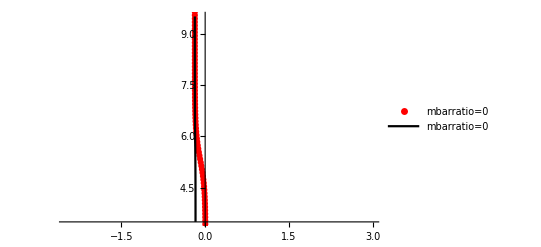

Null

```mathematica
(*Min Error Plots*)
mbarratio0=0;(*competitor/target mRNA levels*) (* keep this zero increase ptot1 prefactor for multi-targets*)
pbarcv0=0*mbarratio0*ptot1;
notarget=1;
ptot1=notarget*ptot1single;  (*upscale for no of targets*)
fanoUNREG00=fanounregfunc[kp1,dp1,dm0,ptot1];
c00v=nm0*dm0*dp1/kp1*(ptot1+pbarcv0);
n00=nm0*dm0*dp1/kp1*(ptot1+pbarcv0);
tabKmin2nuctLIN0=Table[KMMminndaggernum[n00+10^ynuct,kp1,ptot1,dmmu1,dp1,dm0,dmu1,nm0,nmu0,KMMcv,pbarcv0],{ynuct,3.0,9.5,.1}];
tabKmin2nuctLIN0opt=Table[KMMminndaggerOPTnum[n00+10^ynuct,kp1,ptot1,dmmu1,dp1,dm0,dmu1,nm0,nmu0,KMMcv,pbarcv0],{ynuct,3.0,9.5,.1}];
tabErmin2nuct0=Table[{Log10[tabKmin2nuctLIN0[[ii,1]]*noconv],Log10[ppfactor*tabKmin2nuctLIN0[[ii,9]]]},{ii,1,Length[tabKmin2nuctLIN0]}];
tabErmin2nuct0opt=Table[{Log10[tabKmin2nuctLIN0opt[[ii,1]]*noconv],Log10[ppfactor*tabKmin2nuctLIN0opt[[ii,9]]]},{ii,1,Length[tabKmin2nuctLIN0opt]}];
pErmin2nuct0=ListPlot[tabErmin2nuct0,PlotRange->{{-2.5,3},{3.5,9.5}},PlotStyle->Red,PlotLegends->{Row@{"mbarratio=", mbarratio0 },Red}];
pErmin2nuct0opt=ListPlot[tabErmin2nuct0opt,PlotRange->{{-2.5,3},{3.5,9.5}},PlotStyle->Black,Joined->True,PlotLegends->{Row@{"mbarratio=", mbarratio0 },Black}];
Show[pErmin2nuct0,pErmin2nuct0opt]
```

```mathematica
(*Minimum achievable Fano factor*)
tabFmin2nuct0=Table[{Log10[ppfactor*tabKmin2nuctLIN0[[ii,9]]],(tabKmin2nuctLIN0[[ii,4]]-1)/(fanoUNREG00-1)},{ii,1,Length[tabKmin2nuctLIN0]}];
tabFmin2nuct0opt=Table[{Log10[ppfactor*tabKmin2nuctLIN0opt[[ii,9]]],(tabKmin2nuctLIN0opt[[ii,4]]-1)/(fanoUNREG00-1)},{ii,1,Length[tabKmin2nuctLIN0opt]}];
tabFmin2nuct0diff=Table[{Log10[ppfactor*tabKmin2nuctLIN0opt[[ii,9]]],(tabKmin2nuctLIN0[[ii,4]]-tabKmin2nuctLIN0opt[[ii,4]])/(fanoUNREG00-1)},{ii,1,Length[tabKmin2nuctLIN0opt]}];
```

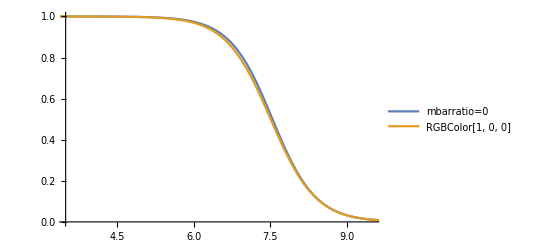

```mathematica
pFmin2nuct0=ListPlot[{tabFmin2nuct0,tabFmin2nuct0opt},PlotRange->{{3.5,9.5},{0,1}},Joined->True,PlotLegends->{Row@{"mbarratio=", mbarratio0 },Red}]
```

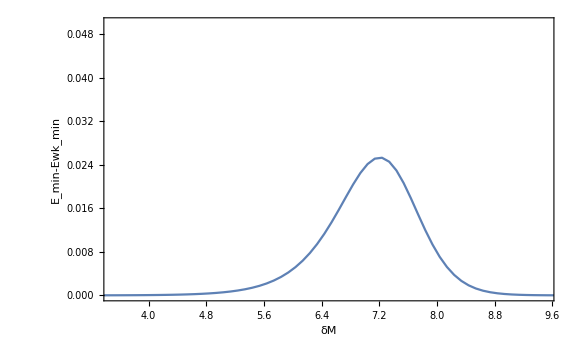

```mathematica
pFmin2nuct0diff=ListPlot[{tabFmin2nuct0diff},PlotRange->{{3.5,9.5},{0,.05}},Joined->True,Frame->True,FrameLabel->{"δM","E_min-Ewk_min"}]
```

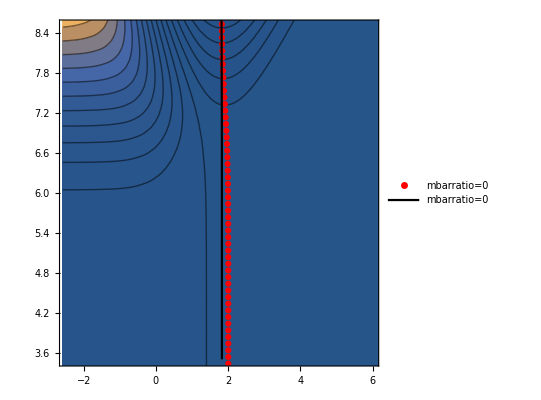

Null

```mathematica
(*Contour Plots*)(*functions always calculate Fano factor, here (FR-1)/(F0-1) contours (yet, almost identical with FR/F0 contours) *)
tabContFano=Flatten[Table[{yKmmvar+Log10[noconv],Log10[ppfactor*(10^ynuct)],(fanofuncmuraw[kp1,ptot1,dp1,dm0,10^yKmmvar,dmmu1,fixNuctgetgammsnum[n00+10^ynuct,kp1,10^yKmmvar,dp1,ptot1,dm0/(dm0+dmmu1),dm0,dmu1,nm0,nmu0,10^yKmmvar,pbarcv0][[4]],dmu1]-1)/(fanoUNREG00-1)},{yKmmvar,0.5,9.5,0.1},{ynuct,3.0,8.5,0.1}],1];
pcontourFano=ListContourPlot[tabContFano,Contours->Table[10^x,{x,-3,3,.2}],PlotRange->All];
Show[pcontourFano,pErmin2nuct0,pErmin2nuct0opt,PlotRange->{{-2.5,6},{3.5,8.5}}]
```

```mathematica
(*to get output data for matplotlib Fig 2*)
tabContFanop=Table[{noconv*10^yKmmvar,ppfactor*(10^ynuct),(fanofuncmuraw[kp1,ptot1,dp1,dm0,10^yKmmvar,dmmu1,fixNuctgetgammsnum[n00+10^ynuct,kp1,10^yKmmvar,dp1,ptot1,dm0/(dm0+dmmu1),dm0,dmu1,nm0,nmu0,10^yKmmvar,pbarcv0][[4]],dmu1]-1)/(fanoUNREG00-1)},{yKmmvar,0.5,9.5,0.1},{ynuct,3.0,9.5,0.1}];
dx=Dimensions[tabContFanop][[1]];
dy=Dimensions[tabContFanop][[2]];
tabContFx=Table[noconv*10^yKmmvar,{yKmmvar,0.5,9.5,0.1}];
tabContFy=Table[ppfactor*(10^ynuct),{ynuct,3.0,9.5,0.1}];
tabContFz=Table[tabContFanop[[ii,jj,3]],{ii,1,dx},{jj,1,dy}];
```

```mathematica
(*to get output data for matplotlib Fig S1*)
tabContFanopdiff=Table[{noconv*10^yKmmvar,ppfactor*(10^ynuct),(fanofuncmuraw[kp1,ptot1,dp1,dm0,10^yKmmvar,dmmu1,fixNuctgetgammsnum[n00+10^ynuct,kp1,10^yKmmvar,dp1,ptot1,dm0/(dm0+dmmu1),dm0,dmu1,nm0,nmu0,10^yKmmvar,pbarcv0][[4]],dmu1]-1)/(foptfuncmuraw2[kp1,ptot1,dp1,dm0,10^yKmmvar,dmmu1,fixNuctgetgammsnum[n00+10^ynuct,kp1,10^yKmmvar,dp1,ptot1,dm0/(dm0+dmmu1),dm0,dmu1,nm0,nmu0,10^yKmmvar,pbarcv0][[4]],dmu1]-1)-1},{yKmmvar,0.5,9.5,0.1},{ynuct,3.0,9.5,0.1}];
dx=Dimensions[tabContFanop][[1]];
dy=Dimensions[tabContFanop][[2]];
tabContFxdiff=Table[noconv*10^yKmmvar,{yKmmvar,0.5,9.5,0.1}];
tabContFydiff=Table[ppfactor*(10^ynuct),{ynuct,3.0,9.5,0.1}];
tabContFzdiff=Table[tabContFanopdiff[[ii,jj,3]],{ii,1,dx},{jj,1,dy}];
```

```mathematica
(*Data Export*)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],StringJoin["mirPD1minC2WKt",ToString[notarget],"txt"]}],tabErmin2nuct0opt,"Table"];
Export[FileNameJoin[{NotebookDirectory[],StringJoin["mirPD1minC2t",ToString[notarget],"txt"]}],tabErmin2nuct0,"Table"];
Export[FileNameJoin[{NotebookDirectory[],StringJoin["mirPD1FxC2t",ToString[notarget],"txt"]}],tabContFx,"Table"];
Export[FileNameJoin[{NotebookDirectory[],StringJoin["mirPD1FyC2t",ToString[notarget],"txt"]}],tabContFy,"Table"];
Export[FileNameJoin[{NotebookDirectory[],StringJoin["mirPD1FzC2t",ToString[notarget],"txt"]}],Transpose[tabContFz],"Table"];
Export[FileNameJoin[{NotebookDirectory[],StringJoin["mirPD1FxC2t",ToString[notarget],"diff.txt"]}],tabContFxdiff,"Table"];
Export[FileNameJoin[{NotebookDirectory[],StringJoin["mirPD1FyC2t",ToString[notarget],"diff.txt"]}],tabContFydiff,"Table"];
Export[FileNameJoin[{NotebookDirectory[],StringJoin["mirPD1FzC2t",ToString[notarget],"diff.txt"]}],Transpose[tabContFzdiff],"Table"];
Export[FileNameJoin[{NotebookDirectory[],StringJoin["mirErrWK",ToString[notarget],"txt"]}],tabFmin2nuct0opt,"Table"];
Export[FileNameJoin[{NotebookDirectory[],StringJoin["mirErrt",ToString[notarget],"txt"]}],tabFmin2nuct0,"Table"];
```